```mathematica
lenetModel=NetModel["LeNet Trained on MNIST Data","UninitializedEvaluationNet"]
```

NetChain[<>]

```mathematica
lenetModelConstructionNotebook= NetModel["LeNet Trained on MNIST Data","ConstructionNotebook"]
```

ig3ix_shm40FrontEndObject[LinkObject["ig3ix_shm", 3, 1]]40Untitled-1

```mathematica
lenetModelConstruction=NetChain[{
ConvolutionLayer[20,{5,5}],
ElementwiseLayer[Ramp],
BatchNormalizationLayer[],
PoolingLayer[{2,2},{2,2}],
ConvolutionLayer[50,{5,5}],
ElementwiseLayer[Ramp],
BatchNormalizationLayer[],
PoolingLayer[{2,2},{2,2}],
LinearLayer[500],
ElementwiseLayer[Ramp],
LinearLayer[1]
},
"Input"->NetEncoder[{"Image",100,"ColorSpace"->"Grayscale"}]
]
```

NetChain[<>]

```mathematica
resNet=NetModel["Dilated ResNet-22 Trained on Cityscapes Data","UninitializedEvaluationNet"]
```

NetGraph[<>]

```mathematica
vgg16Net=NetModel["VGG-16 Trained on ImageNet Competition Data","UninitializedEvaluationNet"]
```

NetChain[<>]

```mathematica
vgg16Net2=NetReplacePart[NetTake[vgg16Net,{"conv1_1","pool5"}],"Input"->NetEncoder[{"Image",100}]]
```

NetChain[<>]

```mathematica
vgg16Net3=NetInsert[vgg16Net2,"b1"->BatchNormalizationLayer[],"conv1_2"]
```

NetChain[<>]

```mathematica
vgg16Net3=NetInsert[vgg16Net3,"b2"->BatchNormalizationLayer[],"conv2_1"]
```

NetChain[<>]

```mathematica
vgg16Net3=NetInsert[vgg16Net3,"b3"->BatchNormalizationLayer[],"conv2_2"]
```

NetChain[<>]

```mathematica
vgg16Net3=NetInsert[vgg16Net3,"b4"->BatchNormalizationLayer[],"conv3_1"]
```

NetChain[<>]

```mathematica
vgg16Net3=NetInsert[vgg16Net3,"b5"->BatchNormalizationLayer[],"conv3_2"]
```

NetChain[<>]

```mathematica
vgg16Net3=NetInsert[vgg16Net3,"b6"->BatchNormalizationLayer[],"conv3_3"]
```

NetChain[<>]

```mathematica
vgg16Net3=NetInsert[vgg16Net3,"b7"->BatchNormalizationLayer[],"conv4_1"]
```

NetChain[<>]

```mathematica
vgg16Net3=NetInsert[vgg16Net3,"b8"->BatchNormalizationLayer[],"conv4_2"]
```

NetChain[<>]

```mathematica
vgg16Net3=NetInsert[vgg16Net3,"b9"->BatchNormalizationLayer[],"conv4_3"]
```

NetChain[<>]

```mathematica
vgg16Net3=NetInsert[vgg16Net3,"b10"->BatchNormalizationLayer[],"conv5_1"]
```

NetChain[<>]

```mathematica
vgg16Net3=NetInsert[vgg16Net3,"b11"->BatchNormalizationLayer[],"conv5_2"]
```

NetChain[<>]

```mathematica
vgg16Net3=NetInsert[vgg16Net3,"b12"->BatchNormalizationLayer[],"conv5_3"]
```

NetChain[<>]

```mathematica
vgg16Net4=NetChain[{vgg16Net3,LinearLayer[15]}]
```

NetChain[<>]

```mathematica
dataDirectory="C:\\Users\\rbc15\\Desktop\\Mathematica\\MLData2\\";
```

```mathematica
ids=Map[FileBaseName,Map[FileNameTake,FileNames[___~~".mx",dataDirectory]]];
```

$Aborted

```mathematica
Export["C:\\Users\\rbc15\\Desktop\\Mathematica\\MLNamesData2.mx",ids]
```

C:\Users\rbc15\Desktop\Mathematica\MLNamesData2.mx

```mathematica
Length[ids]
```

89524

```mathematica
ids=Import["C:\\Users\\rbc15\\Desktop\\Mathematica\\MLNamesData2.mx"]
```

{00002bf3-e652-4937-b5b7-da80bc8794e6,00009198-253e-4028-a689-6a64578d99ea,0000aaf4-d0a7-42b6-9220-2a138237794b,0000dbd4-c3eb-4924-a383-e4207adc3c47,89516,fff8f914-66fb-4f47-ad71-d0e83f75e631,fffa1a96-e4cc-4f42-8af4-8c9f8b968044,fffbedfd-5c1e-4327-8ecf-4fde9cd9a910,fffd69a1-6adb-42d1-8261-544329798314}
 |  |  |  |

```mathematica
mxs=Import["C:\\Users\\rbc15\\Desktop\\Mathematica\\MLData2.mx"]
```

<|00002bf3-e652-4937-b5b7-da80bc8794e6→{35500,37500,6500,1000,28500,26500,50000,22500,39500,24000},00009198-253e-4028-a689-6a64578d99ea→{15500,26000,46500,18500,24000,10000,38500},89521,fffd69a1-6adb-42d1-8261-544329798314→{6500,41000,45000}|>
 |  |  |  |

```mathematica
mxs=AssociationMap[Import[FileNameJoin[{dataDirectory,StringJoin[#,".mx"]}]]&,ids];
```

```mathematica
Export["C:\\Users\\rbc15\\Desktop\\Mathematica\\MLData2.mx",mxs]
```

C:\Users\rbc15\Desktop\Mathematica\MLData2.mx

```mathematica
mxs
```

<|00002bf3-e652-4937-b5b7-da80bc8794e6→{35500,37500,6500,1000,28500,26500,50000,22500,39500,24000},00009198-253e-4028-a689-6a64578d99ea→{15500,26000,46500,18500,24000,10000,38500},89521,fffd69a1-6adb-42d1-8261-544329798314→{6500,41000,45000}|>
 |  |  |  |

```mathematica
data=Flatten[Map[{File[FileNameJoin[{dataDirectory,StringJoin[#,".jpg"]}]]->{mxs[[Key[#]]][[1]]}}&,ids]];
```

```mathematica
sample=RandomSample[testing,10]
```

{File[C:\Users\rbc15\Desktop\Mathematica\MLData2\fd4d709e-ee35-4ca0-b250-73820d7336a4.jpg]→{40500},File[C:\Users\rbc15\Desktop\Mathematica\MLData2\f0555132-44ba-4303-8207-a5c527dfe961.jpg]→{42000},File[C:\Users\rbc15\Desktop\Mathematica\MLData2\f8e3e7fd-ec28-4401-9d55-5054b1031d80.jpg]→{40500},File[C:\Users\rbc15\Desktop\Mathematica\MLData2\ff3127e7-8ae3-49a1-89d8-2b8305ae6dd3.jpg]→{36500},File[C:\Users\rbc15\Desktop\Mathematica\MLData2\f002246b-ecb8-45c4-bb46-a8916b12bd96.jpg]→{27500},File[C:\Users\rbc15\Desktop\Mathematica\MLData2\f0a4f398-62cb-4c34-84da-32b7f2c6b6fb.jpg]→{35000},File[C:\Users\rbc15\Desktop\Mathematica\MLData2\f62729c7-df1c-4c20-83a0-5f6036f263c2.jpg]→{4000},File[C:\Users\rbc15\Desktop\Mathematica\MLData2\f928bfec-9550-48d3-bf12-1491c3560b1c.jpg]→{36000},File[C:\Users\rbc15\Desktop\Mathematica\MLData2\f8637488-475e-42ad-80ea-e02be8cc8e87.jpg]→{21500},File[C:\Users\rbc15\Desktop\Mathematica\MLData2\f666d45f-243a-4264-a544-a3e80edd04d7.jpg]→{40000}}

```mathematica
{training,testing}=TakeDrop[data,83500];
```

```mathematica
NetTrain[vgg16Net4,training,ValidationSet->testing,TargetDevice->"GPU",BatchSize->32]
```

NetChain[<>]

```mathematica
vgg16NetTrained=%
```

NetChain[<>]

```mathematica
vgg16NetTrained[sample[[All,1]]]
sample[[All,2]]
```

{{38730.1},{39501.2},{40576.6},{36069.7},{26559.1},{34887.6},{3011.72},{36565.5},{20769.4},{40259.6}}

{{40500},{42000},{40500},{36500},{27500},{35000},{4000},{36000},{21500},{40000}}

```mathematica
vgg16NetTrained[{-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{{20092.9},{20960.1},{13597.1},{20941.7}}

```mathematica
listData=Flatten[Map[{File[FileNameJoin[{dataDirectory,StringJoin[#,".jpg"]}]]->class[mxs[[Key[#]]],20]}&,ids]];
```

```mathematica
class[list_,nbins_]:=Map[Floor[(#/Max[list])*nbins]&,list]
```

```mathematica
{traininglist,testinglist}=TakeDrop[listData,81000];
```

```mathematica
loss=CTCLossLayer[]
```

CTCLossLayer[<>]

```mathematica
classes=Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
decoder=NetDecoder[{"CTCBeamSearch",classes}]
```

NetDecoder[<>]

```mathematica
ocrNet=NetChain[{ConvolutionLayer[20,3],BatchNormalizationLayer[],Ramp,PoolingLayer[2],ConvolutionLayer[15,3],BatchNormalizationLayer[],Ramp,PoolingLayer[2],FlattenLayer[1],TransposeLayer[],GatedRecurrentLayer[19],GatedRecurrentLayer[19],NetMapOperator[LinearLayer[Length[classes]+1]],SoftmaxLayer[]},"Input"->NetEncoder[{"Image",100,"Grayscale"}],"Output"->decoder]
```

NetChain[<>]

```mathematica
ocrNetTrained=NetTrain[ocrNet,traininglist,ValidationSet->testinglist,LossFunction->loss,BatchSize->32,TargetDevice->"GPU"]
```

NetChain[<>]

```mathematica
samplelist=RandomSample[testinglist,10];
```

```mathematica
predictions=ocrNetTrained[samplelist[[All,1]]]
```

{{13,18,10,19,4,12,11,1,8,10,6,20,4,11},{7,12,20,16,13,8},{11,3,15,5,20},{16,20},{20,7,9,13,18,9,16,15,5,20,10,11},{18,20,9,8,6,19},{20},{20,17},{8,12,15,10,12,1,7,20,9,15,5,9},{9,15,18,5,19,20,1,10,3,12,18}}

```mathematica
solutions=samplelist[[All,2]]
```

{{13,18,10,19,4,13,11,2,9,11,7,20,5,12},{7,12,20,15,13,13,8,0},{11,3,15,5,20},{16,20},{20,6,9,13,13,18,10,16,15,5,19,10,10},{18,20,9,8,0,5,19},{20},{20,17},{8,12,1,14,10,12,15,1,7,7,20,9,15,5,10},{9,15,17,1,5,19,20,1,10,1,3,12,18}}

```mathematica
Map[Import,samplelist[[All,1]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

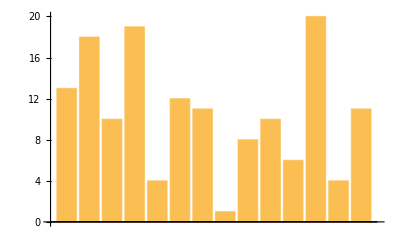
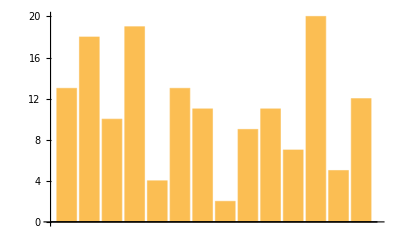
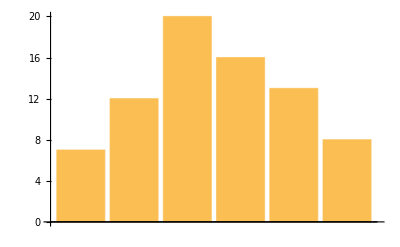
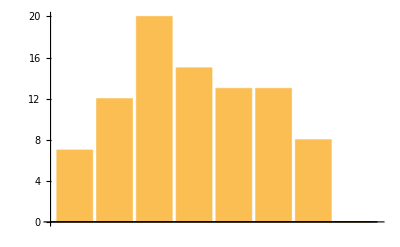
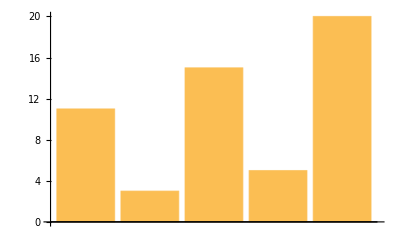
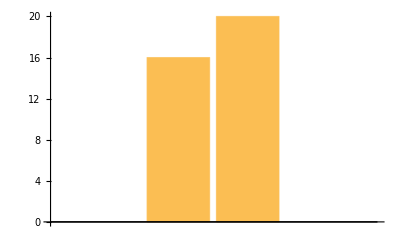
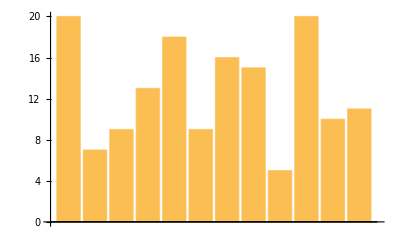
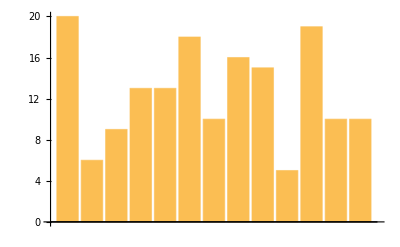
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
transposed=Transpose[{Map[BarChart[#]&,predictions],Map[BarChart[#]&,solutions]}]
```

variable length images

```mathematica
ocrNetTrained[-Graphics-,{"TopDecodings",5}]
```

{{4,3,4,6,17,16,19,20,19,20,10,9,19,16,15},{4,3,4,6,17,16,19,20,19,20,10,9,19,16,15},{4,3,4,6,17,16,20,19,20,10,9,19,16,15},{4,3,4,6,17,16,20,19,20,10,9,19,16,15},{4,5,4,6,17,16,19,20,19,20,10,9,19,16,15}}

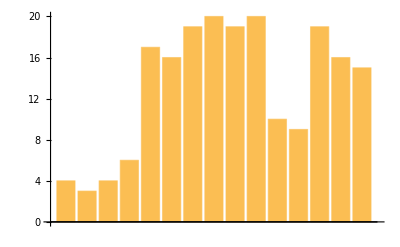
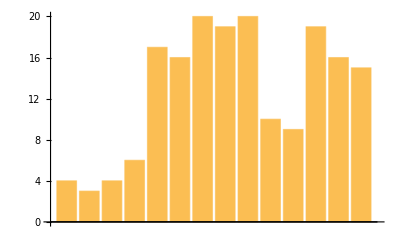
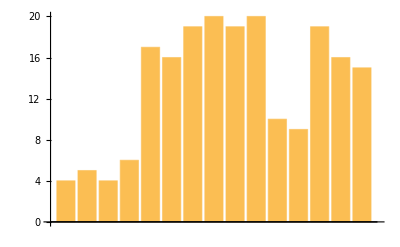
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[BarChart[#]&,%]
```

```mathematica
BarChart[{4,3,4,6,17,16,19,20,19,20,10,9,19,16,15}]
```

-Graphics-